```mathematica
data1a = Transpose@ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig1/ave_ipr.csv"]][[2;;-1]];
```

```mathematica
data1b = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig1/phase_ipr.csv"]][[2;;-1]];
```

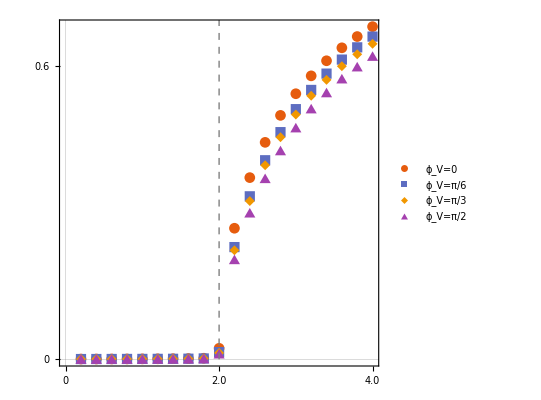

```mathematica
fig1a = Show[ListPlot[data1a, PlotTheme->"Scientific", FrameTicks->{{{0, 0.6},None},{{0,{10,"2.0"},{20,"4.0"}},None}}, LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},PlotMarkers->Automatic,PlotLegends->Placed[{"ϕ_V=0", "ϕ_V=π/6", "ϕ_V=π/3", "ϕ_V=π/2"}, {Left, 0.5}],(*FrameLabel->{Row[{"λ"}],Row[{ "Average IPR"}]},*) AspectRatio->1, ImageSize->{295}], Graphics[{Dashed, Gray,Line[{{10,-.1},{10,1}}]}]]
```

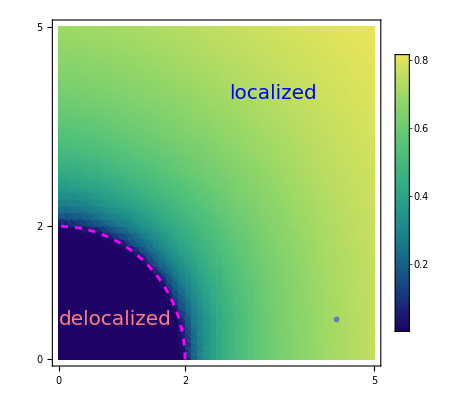

```mathematica
fig1b = Show[ListDensityPlot[data1b,ColorFunction->ColorData["BlueGreenYellow"],(*FrameLabel->{Row[{"Re ",Style["E",Italic]}],Row[{ "Im ",Style["E",Italic]}]},*)FrameTicks->{{{0,{1, "2"},{2.5, "5"}},None},{{0,{1, "2"},{2.5, "5"}},None}},PlotLegends->Placed[BarLegend[Automatic, LegendMarkerSize->{15, 200},(*Ticks->{0.0,0.8},*)LabelStyle->{FontFamily->"Times New Roman",18,Black}], Right], PlotRangePadding->None,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}, ImageSize->{300}, Epilog->{Inset[Style["delocalized",20,FontFamily->Times, Pink],{.45,0.3}],Inset[Style["localized",20,FontFamily->Times, Blue],{1.7,2}]}],ListPlot[List /@ {{2.2,.3}},PlotMarkers->{Graphics3D[{RGBColor[1,1,1,0],Sphere[]},Boxed->False],6}],ParametricPlot[{Cos[t],Sin[t]},{t,0,Pi/2}, PlotStyle->{RGBColor[1,0,1], Dashed}]]
```

```mathematica
Fig1 = ListPlot[{{0,0}},PlotStyle->Opacity[0],PlotRange->{{0,1},{0,1}},ImageSize->{660,Automatic},Axes->None,Epilog->{Inset[fig1a,{.225,0.51}], Inset[fig1b,{.735,0.52}],Inset[Rotate[Row[{Style["Im ",23,FontFamily->"Times"],Style["V",23,FontFamily->"Times",Italic]}],Pi/2],{0.47,0.59}],Inset[Rotate[Row[{Style["Average IPR",23,FontFamily->"Times"]}],Pi/2],{0.03,0.5}], Inset[Row[{Style["Re ",23,FontFamily->"Times"],Style["V",23,FontFamily->"Times",Italic]}], {0.71, 0.04}],Inset[Row[{Style["|V|",23,FontFamily->"Times"]}], {0.245, 0.04}], Inset[Row[{Style["IPR",18,FontFamily->"Times"]}], {0.93, 0.85}],Inset[Style["(a)",26,FontFamily->Times],{.08,0.9}],Inset[Style["(b)",26,FontFamily->Times],{.527,0.9}]}, AspectRatio->0.47]
```

-Graphics-

```mathematica
Export["/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig1/Fig1.pdf",Fig1,"PDF"]
```

/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig1/Fig1.pdf